## Limitations of a linear shutter ramp

Linear ramp function

```mathematica
(* Exposure time as a linear function of frame number F, with initial exposure, final exposure, frame count as parameters  *)
(* Note: F is inputted in the 1:F domain but calculations are done in the 0:F domain. Input the actual frame number *)
ExposureTimeAtFrameF[F_,initExpSec_,finExpSec_,frames_]:=(finExpSec-initExpSec)/frames((frames(F-1))/(frames-1))+initExpSec
```

Assumed environment brightness as a function of angular distance of Sun from zenith (0°)

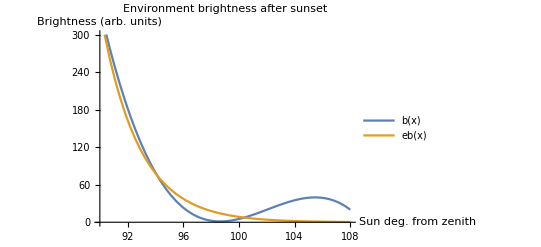

```mathematica
(* From sunset to end of astronomical twilight *)
(* b[x] is a cubic spline constructed from ephemeris data found online *)
(* eb[x] is a decaying exponential curve that roughly matches b[x]  *)
b[x_]:=-0.24170462x^3+74.006284x^2-7544.765x+256103.54+20;
eb[x_]:=340Exp[-(x-90)/Exp[1]];
SetOptions[Plot,ImageSize->{400,180}];
Plot[{b[x],eb[x]},{x,90,108},AxesOrigin->{90,0},PlotRange->{0,300},AxesLabel->{"Sun deg. from zenith","Brightness (arb. units)"},PlotLabel->"Environment brightness after sunset",LabelStyle->{GrayLevel[0]},PlotLegends->"Expressions"]
```

Computations

```mathematica
(* Total elapsed time is the summation of exposure times from frame A to B *)
RealWorldTimeBetweenFramesAandB[A_,B_,pause_,initExpSec_,finExpSec_,frames_]:=∑_(k=A)^B (ExposureTimeAtFrameF[k,initExpSec,finExpSec,frames]+pause)
```

```mathematica
(* Brightness of environment as a function of frame number *)
SceneBrightnessAtFrameF[F_,sunsetTimeSec_,initExpSec_,finExpSec_,frames_,pause_]:=Piecewise[{{eb[x], 90≤x≤108}, {0, True}}]/.{x->(((18 RealWorldTimeBetweenFramesAandB[1,F,pause,initExpSec,finExpSec,frames]-sunsetTimeSec)/(4320+sunsetTimeSec))+90)}
```

```mathematica
(* Image brightness = (area) * (iso speed) * (exposure time) * (scene brightness) *)
ImageBrightnessAtFrameF[F_,sunsetTimeSec_,initExpSec_,finExpSec_,frames_,pause_,isoSpeed_,apertureArea_]:=(apertureArea) (isoSpeed)(SceneBrightnessAtFrameF[F,sunsetTimeSec,initExpSec,finExpSec,frames,pause]) (ExposureTimeAtFrameF[F,initExpSec,finExpSec,frames])
```

Parameters from 3-26-19 timelapse, 7:27 PM to 9:55 PM

```mathematica
(* number of frames *)
fr=409;

(* initial exposure, final exposure (sec) *)
 init=0.1; fin=42;

(* time between end of one frame and beginning of next (sec) *)
p=0.5;

(* sensor sensitivity and aperture area in mm^2 *)
iso=100;
area=0.004751;
```

Plot 1: The ratio of successive exposure times grows

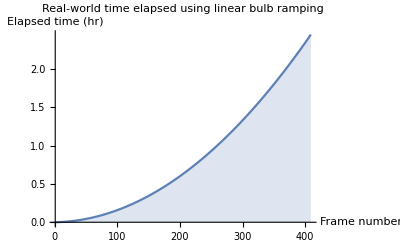

```mathematica
plot1=Show[DiscretePlot[1/3600 RealWorldTimeBetweenFramesAandB[1,k,p,init,fin,fr],{k,1,fr}],
AxesLabel->{"Frame number","Elapsed time (hr)"},PlotLabel->"Real-world time elapsed using linear bulb ramping",LabelStyle->{GrayLevel[0]}]
```

Plot 2: How bright we expect the environment to be with each frame

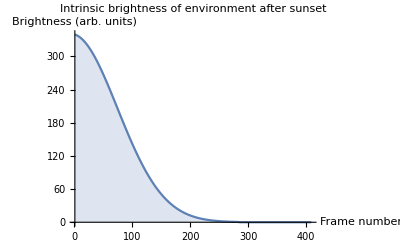

```mathematica
plot2=Show[DiscretePlot[SceneBrightnessAtFrameF[k,0,init,fin,fr,p],{k,1,fr}],
AxesLabel->{"Frame number","Brightness (arb. units)"},PlotLabel->"Intrinsic brightness of environment after sunset",LabelStyle->{GrayLevel[0]}]
```

Plot 3:  How bright we expect each frame to be when using a linear ramp

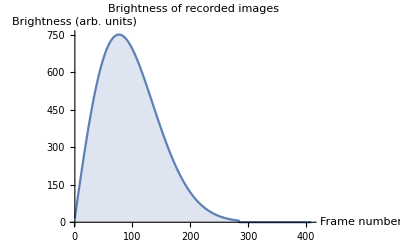

```mathematica
(* What we expect the brightness of each frame to be when we use a linear ramp *)
plot3=Show[DiscretePlot[ImageBrightnessAtFrameF[k,0,init,fin,fr,p,iso,area],{k,1,fr}],
AxesLabel->{"Frame number","Brightness (arb. units)"},PlotLabel->"Brightness of recorded images",LabelStyle->{GrayLevel[0]}]
```